```mathematica
Remove["iswap"]
```

Remove::rmnsm: There are no symbols matching ""iswap"".

```mathematica
iswap[α_] := {{1,0,0,0},{0,Cos[α/2],-I Sin[α/2],0},{0,-I Sin[α/2],Cos[α/2],0},{0,0,0,1}}
```

```mathematica
rx[α_]={{Cos[α/2],-I Sin[α/2]},{-I Sin[α/2],Cos[α/2]}};
```

```mathematica
ry[α_]={{Cos[α/2],-Sin[α/2]},{Sin[α/2],Cos[α/2]}};
```

```mathematica
rz[α_]={{Exp[-ⅈ α/2],0},{0,Exp[ⅈ α/2]}};
```

```mathematica
inversionAboutAverage = KroneckerProduct[rx[π/2],rx[π/2]].iswap[π]
```

{{1/2,-1/2,-1/2,-1/2},{-ⅈ/2,ⅈ/2,-ⅈ/2,-ⅈ/2},{-ⅈ/2,-ⅈ/2,ⅈ/2,-ⅈ/2},{-1/2,-1/2,-1/2,1/2}}

```mathematica
initialState[d_] := Table[1/Sqrt[d],{i,1,d}];
```

```mathematica
DD[x_] :=(Table[2/Length[x],{i,1,Length[x]},{j,1,Length[x]}]-IdentityMatrix[Length[x]]).x
Oracle[x_,j_] := Table[If[i≠j,x[[i]],-x[[i]]],{i,1,Length[x]}]
```

```mathematica
d = 4;
j = 2;
initialStateX = initialState[d];
DDX = Table[2/d,{i,1,d},{j,1,d}]-IdentityMatrix[d];
stateVectors = FoldList[DDX.Oracle[#1,j]&,initialStateX,Range[1,20]];
```

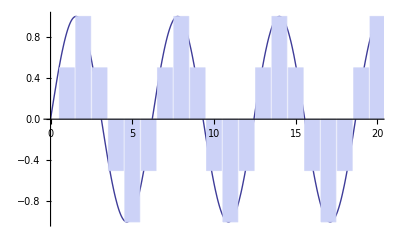

```mathematica
Show[Plot[Sin[x/(Sqrt[4]*π/4)*π/2*1.01],{x,0,20}],BarChart[Map[#[[j]]&,stateVectors]]]
```

```mathematica
inversionAboutAverage.Oracle[initialState[4],4]
```

{0,0,0,-1}

```mathematica
inversionAboutAverage.KroneckerProduct[rz[-π/2],rz[π/2]].iswap.initialState[4]
```

{{1/2,-ⅈ/2,ⅈ/2,-1/2},{-ⅈ/2,-1/2,-1/2,-ⅈ/2},{-ⅈ/2,1/2,1/2,-ⅈ/2},{-1/2,-ⅈ/2,ⅈ/2,1/2}}.iswap.{1/2,1/2,1/2,1/2}

```mathematica
KroneckerProduct[rz[-π/2],rz[π/2]].iswap[0.1].initialState[4]
```

{0.5+0. ⅈ,0.0249896+0.499375 ⅈ,-0.0249896-0.499375 ⅈ,0.5+0. ⅈ}

```mathematica
n= 4
DiffusionMatrix = Table[If[Or[i-j == 1,i-j==-1,i-j == n-1,j-i == n-1],I ϵ,If[i==j,1-2I ϵ,0]],{i,1,4},{j,1,4}]
PotentialMatrix = Table[If[i==j,If[i==1,Exp[-I γ],1],0],{i,1,4},{j,1,4}]
```

4

{{1-2 ⅈ ϵ,ⅈ ϵ,0,ⅈ ϵ},{ⅈ ϵ,1-2 ⅈ ϵ,ⅈ ϵ,0},{0,ⅈ ϵ,1-2 ⅈ ϵ,ⅈ ϵ},{ⅈ ϵ,0,ⅈ ϵ,1-2 ⅈ ϵ}}

{{ⅇ^(-ⅈ γ),0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
DiffusionMatrix // MatrixForm
PotentialMatrix // MatrixForm
```

(1-2 ⅈ ϵ | ⅈ ϵ | 0 | ⅈ ϵ
ⅈ ϵ | 1-2 ⅈ ϵ | ⅈ ϵ | 0
0 | ⅈ ϵ | 1-2 ⅈ ϵ | ⅈ ϵ
ⅈ ϵ | 0 | ⅈ ϵ | 1-2 ⅈ ϵ)

(ⅇ^(-ⅈ γ) | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
eigenvals = Eigenvalues[DiffusionMatrix.PotentialMatrix];
```

```mathematica
eigenvecs=Eigenvectors[DiffusionMatrix.PotentialMatrix];
```

```mathematica
parameters = {ϵ->0.01,γ->-1}

MM =(PotentialMatrix.DiffusionMatrix) /. parameters;
MM // MatrixForm
m = 200;
stateVectors = FoldList[(#1/Norm[#1]).MM&,initialState[4],Range[1,m]] ;
Abs[stateVectors[[m]]]
```

{ϵ→0.01,γ→-1}

(0.557132+0.830665 ⅈ | -0.00841471+0.00540302 ⅈ | 0 | -0.00841471+0.00540302 ⅈ
0.+0.01 ⅈ | 1.-0.02 ⅈ | 0.+0.01 ⅈ | 0
0 | 0.+0.01 ⅈ | 1.-0.02 ⅈ | 0.+0.01 ⅈ
0.+0.01 ⅈ | 0 | 0.+0.01 ⅈ | 1.-0.02 ⅈ)

{0.527793,0.481202,0.508478,0.481202}

```mathematica
initialState[4].PotentialMatrix.DiffusionMatrix
```

{1/2 γ (1-2 ϵ)+ϵ,1/2 (1-2 ϵ)+ϵ/2+(γ ϵ)/2,1/2 (1-2 ϵ)+ϵ,1/2 (1-2 ϵ)+ϵ/2+(γ ϵ)/2}

```mathematica
Abs[eigenvals]^10 /.parameters
```

{0.107374,0.0927748,0.0134163,0.521613}